## Linked Micro-swimmers 2 Spheres, 1 Active Link, Harmonic

```mathematica
ClearAll["Global`*"]
```

## Setting up Model System

```mathematica
Clear[R1, R2, μ, mob1, mob2]
mob1 = 1/(6 π μ R1);
mob2 =1/(6 π μ R2);

Clear[unitn, nn, Imnn]
unitn = {1, 0, 0};
nn = Outer[Times, unitn, unitn];
Imnn = IdentityMatrix[3] - nn;

Clear[L1, p12]
p12 = L1;

Clear [f1, f2, Fv1, Fv2]
Fv1 = {f1, 0, 0};
Fv2 = {f2, 0, 0};

Clear[λ12, λ21]
λ12 = R1 / p12;
λ21 = R2 / p12;

Clear[A11, A12, A21, A22]
Clear[B11, B12, B21, B22]
A11 = A22 = B11 = B22 =1;
A12  = 3/2 λ12;
A21  = 3/2 λ21;
B12  = 3/4 λ12;
B21  = 3/4 λ21;
Clear[H11, H12, H21, H22]
H11 = mob1 (A11 nn + B11 Imnn);
H22 = mob2 (A22 nn + B22 Imnn);
H12 =mob1 (A12 nn + B12 Imnn);
H21 =mob2 (A21 nn + B21 Imnn);

Clear[v1, v2]
v1 = (H11.Fv1 + H12.Fv2)[[1]] /. f2 -> -f1;
v2 = (H21.Fv1 + H22.Fv2)[[1]] /. f2 -> -f1;

Clear[L1dot,L1DOT]
L1dot = v2 - v1;

Clear[f1solved, f2solved, v1solved, v2solved, vssolved]
f1solved =(Solve[L1dot == L1DOT, {f1}] // Flatten)[[1,2]] ;
f2solved = - f1solved;
v1solved = v1 /. {f1->f1solved} //Simplify;
v2solved = v2 /. {f1->f1solved}//Simplify;
vssolved = 1/2 (v1solved + v2solved) // Simplify;
```

## Non - Dimensionalization of Model

```mathematica
Clear[l, l1, d1]
Clear[Lchar, Tchar, Vchar, Fchar, Tcycle]
Lchar = l;
Tchar = Tcycle;
Vchar = Lchar/Tchar;
Fchar = Vchar / mob2;

Clear[r1, r2, x1, L1star,L1DOTstar,T,e1]
R1 = Lchar r1;
R2 = Lchar r2;
L1 = Lchar L1star;
L1DOT = Vchar L1DOTstar;
t = Tchar T;
l1 = Lchar x1;
d1 = Lchar e1;

Clear[V1star, V2star, VSstar, F1star, F2star]

V1star = v1solved / Vchar // Simplify;
V2star = v2solved / Vchar // Simplify;
VSstar = vssolved / Vchar // Simplify;
F1star = f1solved / Fchar // Simplify;
F2star = f2solved / Fchar // Simplify;
```

## Defining Deformation Mechanism

```mathematica
Clear[u1]
L1star = x1 + e1 u1[t];
L1DOTstar = D[L1star, T];
```

```mathematica
Clear[ω]
u1[t_] := -Cos[ω t];
Tcycle = 2π / ω;
```

```mathematica
l = 1;
ω = 1;
```

## Analysis of Mechanics within a cycle

```mathematica
Clear[r1,r2, r3, x2, e1, e2]
r1 = 0.25;
r2 = 0.5;
x1 = 1;
e1 = 0.2;

τ1 = 0;
τ2 = 0.125;
τ3 = 0.25;
τ4 = 0.375;
τ5 = 0.5;
τ6 = 0.625;
τ7 = 0.75;
τ8 = 0.875;
τ9 = 1;
```

### Full Cycle Analysis (T goes from 0 to 1)

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in T near {T} = {0.99999615071571260003527542668116945279166429827455431222915649414}. NIntegrate obtained -5.14996×10^-17 and 2.09201×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in T near {T} = {0.99999615071571260003527542668116945279166429827455431222915649414}. NIntegrate obtained -1.42302×10^-19 and 2.19158×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in T near {T} = {0.99999615071571260003527542668116945279166429827455431222915649414}. NIntegrate obtained -1.29562×10^-17 and 1.05408×10^-16 for the integral and error estimates.

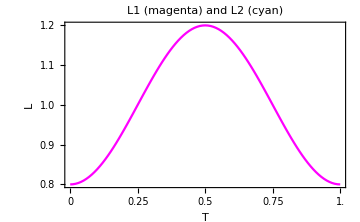

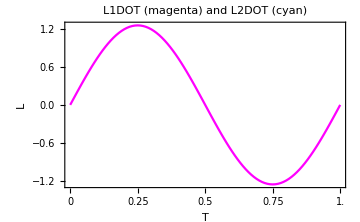

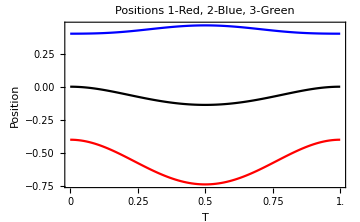

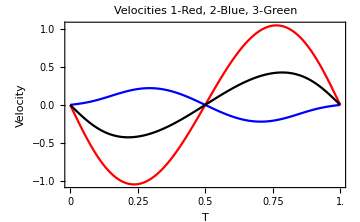

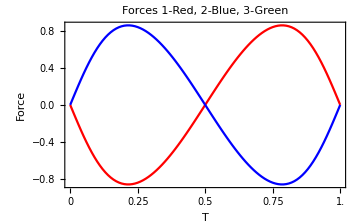

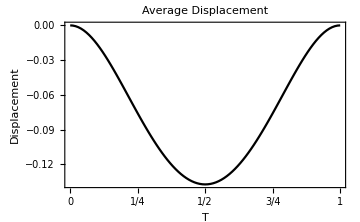

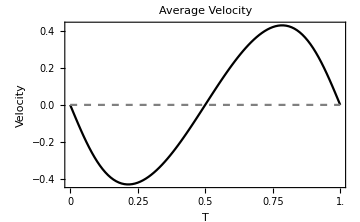

-1.29562×10^-17

```mathematica
Tmin = 0;
Tmax = 1;
Tdiff = (Tmax - Tmin)/100;

L1Data = Table[L1star, {T, Tmin, Tmax, Tdiff}];
L1DOTData = Table[L1DOTstar, {T, Tmin, Tmax, Tdiff}];

V1Data = Table[V1star, {T, Tmin, Tmax, Tdiff}];
V2Data = Table[V2star, {T, Tmin, Tmax, Tdiff}];
VSData = Table[VSstar, {T, Tmin, Tmax, Tdiff}];
F1Data = Table[F1star, {T, Tmin, Tmax, Tdiff}];
F2Data = Table[F2star, {T, Tmin, Tmax, Tdiff}];

D1Data = Table[ NIntegrate[V1star, {T, Tmin, τ}], {τ, Tmin, Tmax, Tdiff}];
D2Data = Table[ NIntegrate[V2star, {T, Tmin, τ}], {τ, Tmin, Tmax, Tdiff}];
DSData = Table[ NIntegrate[VSstar, {T, Tmin, τ}], {τ, Tmin, Tmax, Tdiff}];

AvgV = 1/(Tmax - Tmin)NIntegrate[VSstar, {T, Tmin, Tmax}];

P1Data = (- L1Data[[1]])/2 + D1Data;
P2Data = (+ L1Data[[1]])/2+ D2Data;

Show[
ListLinePlot[L1Data,DataRange -> {Tmin, Tmax},PlotStyle-> {Magenta}],
PlotRange -> All,
Frame -> True,
FrameStyle -> {Black, Thick},
FrameTicks -> {{All, None}, {{Tmin + 0 Tdiff, Tmin +12.5Tdiff, Tmin +25.0Tdiff, Tmin +37.5Tdiff, Tmin +50.0Tdiff, Tmin +62.5Tdiff, Tmin +75.0Tdiff, Tmin +87.5Tdiff, Tmin +100.0Tdiff}, None}},
ImageSize-> Medium,
PlotLabel -> Style["L1 (magenta) and L2 (cyan)", Black, Bold, Italic],
FrameLabel -> {Style["T", Black, Bold],Style[ "L", Black, Bold]}
]
Show[
ListLinePlot[L1DOTData,DataRange -> {Tmin, Tmax},PlotStyle-> {Magenta}],
PlotRange -> All,
Frame -> True,
FrameStyle -> {Black, Thick},
FrameTicks -> {{All, None}, {{Tmin + 0 Tdiff, Tmin +12.5Tdiff, Tmin +25.0Tdiff, Tmin +37.5Tdiff, Tmin +50.0Tdiff, Tmin +62.5Tdiff, Tmin +75.0Tdiff, Tmin +87.5Tdiff, Tmin +100.0Tdiff}, None}},
ImageSize-> Medium,
PlotLabel -> Style["L1DOT (magenta) and L2DOT (cyan)", Black, Bold, Italic],
FrameLabel -> {Style["T", Black, Bold],Style[ "L", Black, Bold]}
]
Show[
ListLinePlot[P1Data,DataRange -> {Tmin, Tmax},PlotStyle-> {Red}],
ListLinePlot[P2Data,DataRange -> {Tmin, Tmax},PlotStyle-> {Blue}],
ListLinePlot[DSData,DataRange -> {Tmin, Tmax},PlotStyle-> {Black}],
PlotRange -> All,
Frame -> True,
FrameStyle -> {Black, Thick},
FrameTicks -> {{All, None}, {{Tmin + 0 Tdiff, Tmin +12.5Tdiff, Tmin +25.0Tdiff, Tmin +37.5Tdiff, Tmin +50.0Tdiff, Tmin +62.5Tdiff, Tmin +75.0Tdiff, Tmin +87.5Tdiff, Tmin +100.0Tdiff}, None}},
ImageSize-> Medium,
PlotLabel -> Style["Positions 1-Red, 2-Blue, 3-Green", Black, Bold, Italic],
FrameLabel -> {Style["T", Black, Bold],Style[ "Position", Black, Bold]}
]
Show[
ListLinePlot[V1Data,DataRange -> {Tmin, Tmax},PlotStyle-> {Red}],
ListLinePlot[V2Data,DataRange -> {Tmin, Tmax},PlotStyle-> {Blue}],
ListLinePlot[VSData,DataRange -> {Tmin, Tmax},PlotStyle-> {Black}],
PlotRange -> All,
Frame -> True,
FrameStyle -> {Black, Thick},
FrameTicks -> {{All, None}, {{Tmin + 0 Tdiff, Tmin +12.5Tdiff, Tmin +25.0Tdiff, Tmin +37.5Tdiff, Tmin +50.0Tdiff, Tmin +62.5Tdiff, Tmin +75.0Tdiff, Tmin +87.5Tdiff, Tmin +100.0Tdiff}, None}},
ImageSize-> Medium,
PlotLabel -> Style["Velocities 1-Red, 2-Blue, 3-Green", Black, Bold, Italic],
FrameLabel -> {Style["T", Black, Bold],Style[ "Velocity", Black, Bold]}
]
Show[
ListLinePlot[F1Data,DataRange -> {Tmin, Tmax},PlotStyle-> {Red}],
ListLinePlot[F2Data,DataRange -> {Tmin, Tmax},PlotStyle-> {Blue}],
PlotRange -> All,
Frame -> True,
FrameStyle -> {Black, Thick},
FrameTicks -> {{All, None}, {{Tmin + 0 Tdiff, Tmin +12.5Tdiff, Tmin +25.0Tdiff, Tmin +37.5Tdiff, Tmin +50.0Tdiff, Tmin +62.5Tdiff, Tmin +75.0Tdiff, Tmin +87.5Tdiff, Tmin +100.0Tdiff}, None}},
ImageSize-> Medium,
PlotLabel -> Style["Forces 1-Red, 2-Blue, 3-Green", Black, Bold, Italic],
FrameLabel -> {Style["T", Black, Bold],Style[ "Force", Black, Bold]}
]
Show[
ListLinePlot[DSData,DataRange -> {Tmin, Tmax},PlotStyle-> {Black}],
PlotRange -> All,
Frame -> True,
FrameStyle -> {Black, Thick},
FrameTicks -> {{All, None}, {{Tmin + 0 Tdiff, Tmin +12.5Tdiff, Tmin +25Tdiff, Tmin +37.5Tdiff, Tmin +50Tdiff, Tmin +62.5Tdiff, Tmin +75Tdiff, Tmin +87.5Tdiff, Tmin +100Tdiff}, None}},
ImageSize-> Medium,
PlotLabel -> Style["Average Displacement", Black, Bold, Italic],
FrameLabel -> {Style["T", Black, Bold],Style[ "Displacement", Black, Bold]}
]
Show[
ListLinePlot[VSData,DataRange -> {Tmin, Tmax},PlotStyle-> {Black}],
ListLinePlot[AvgV + Table[0, {T, Tmin, Tmax, Tdiff}], DataRange->{Tmin,Tmax}, PlotStyle->{Dashed, Gray}],
PlotRange -> All,
Frame -> True,
FrameStyle -> {Black, Thick},
FrameTicks -> {{All, None}, {{Tmin + 0 Tdiff, Tmin +12.5Tdiff, Tmin +25.0Tdiff, Tmin +37.5Tdiff, Tmin +50.0Tdiff, Tmin +62.5Tdiff, Tmin +75.0Tdiff, Tmin +87.5Tdiff, Tmin +100.0Tdiff}, None}},
ImageSize-> Medium,
PlotLabel -> Style["Average Velocity", Black, Bold, Italic],
FrameLabel -> {Style["T", Black, Bold],Style[ "Velocity", Black, Bold]}
]
AvgV
```